# BBM92 protocol

DESCRIPTION: Implementing the finite key BBM92 protocol. Improve existing key rates by using an updated sampling bound to replace previous use of the Serfling bound. 

Analysis based on:
Security Analysis of Quantum Key Distribution with Small Block Length and Its Application to Quantum Space Communications, Lim, Xu, Pan, Ekert, Phys. Rev. Lett. 126 (2021).

Approach: GLOBAL OPTIMISATION OVER FOUR_PARAMETER SPACE. 

Date: 02nd February 2025
Author: Jasminder Sidhu

```mathematica
(*Define the log function*)
h2[0|0.]=0;
h2[x_]:=-x Log2[x]-(1-x) Log2[1-x];
SetAttributes[h2,Listable]

FiniteRateOpt={{"FKL","FKR(alpha)","m","s","beta","nu","xi"}};
Do[
δ=0.0455;
s=6;
r=1.19 h2[δ];

k[β_,m_]:=β m;
n[β_,m_]:=m-k[β,m];
t[s_]:=-Log2[10^(- (s+2))];

Γ[x_,m_]:= 1/(x+1) + 1/(m-x+1);
ϵpe[β_, ν_, ξ_, m_]:= (Exp[-(2m k[β,m] ξ^2)/(n[β,m]+1)]+Exp[-2 Γ[m (δ + ξ),m] (n[β,m]^2 (ν - ξ)^2 - 1)])^(1/2);
ϵpa[β_,ν_,m_,α_]:= 1/2 √(2^(-n[β,m] (1-h2[δ+ν]-r) + t[s] + α m));

C1[α_, β_, ν_, ξ_]:=10^(- (s+2))+ 2 ϵpe[β, ν, ξ, m] + ϵpa[β,ν,m,α] <= 10^-s;
C2=0<α<=1;
C3=0<β<=1/2;
C4=0<ξ<ν<1/2-δ;

C5new=0<ξ<1/2-δ;
C6new=0<ν<1/2-δ;
C7new=ν>ξ;


(*Optimisation variable vector*)
optimisationvariables={α,β,ν,ξ};

FKL= NMaximize[{α,C1[α,β,ν,ξ], C2, C3,C4,C5new,C6new,C7new},optimisationvariables,Method->{"RandomSearch","SearchPoints"->150}]//Quiet;

maxRate=Max[0,FKL[[1]]];
beta=FKL[[2,2,2]];
nu=FKL[[2,3,2]];
xi=FKL[[2,4,2]];

AppendTo[FiniteRateOpt, {m maxRate, maxRate,m,s,beta,nu,xi}],{m,3000,8000,100}];
```

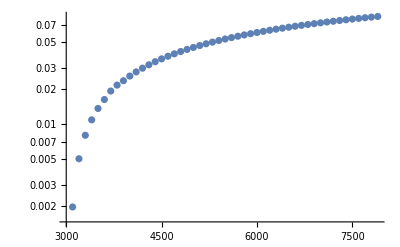

```mathematica
ListLogPlot[FiniteRateOpt[[All,{3,2}]][[3;;-2]]]
```